```mathematica
(*Этот блок строит численное решение на отрезке*)
L=1; (*Длина отрезка*)
Tv=5; (*Время*)
n=100; (*Количество точек по пространству*)
m=10000; (*Количество точек по времени*)
kappa=0.01; (*Коэффициент теплопроводности*)

dx=L/n;
dt=Tv/m;
r=dt/(dx*dx)

(*Начальные и граничные условия*)
T0[x_]:=0;
Tleft[t_]:=1; (*Температура на левой границе*)
Tright[t_]:=0; (*Температура на правой границе*)


T=Table[0,{m+1},{n+1}]; (*Для хранения температуры*)

(**)
T[[1]]=Table[T0[i*dx],{i,0,n}];
Do[
T[[i+1,1]]=Tleft[i*dt];
T[[i+1,n+1]]=Tright[i*dt];
Do[
T[[i+1,j]]=T[[i,j]]+kappa*dt/dx^2*(T[[i,j-1]]-2*T[[i,j]]+T[[i,j+1]]);,{j,2,n}
];,{i,1,m}
];

(*
ListPlot3D[T,DataRange->{{0,L},{0,Tv},Automatic},PlotRange->All,AxesLabel->{"x","t","T"}]*)
```

5

```mathematica
(*В этом блоке можно посмотреть график распределения температур в разные моменты времени*)
Manipulate[
ListPlot[Table[T[[tau,i]],{i,1,n}],DataRange->{0,L},PlotRange->{{0,1},{0,1}},AxesLabel->{"x","T"},
GridLines->Automatic,Joined->True,PlotLegends->tau*dt]
,
{{tau,m/2},1,m}
]
```

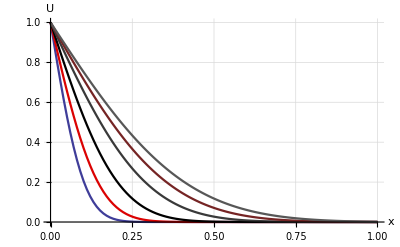

{5/16,5/8,5/4,5/2,15/4,5}

```mathematica
(*Строит графики распределения температуры в несколько моментов времени списка time*)
time={m/16,m/8,m/4,m/2,3m/4,m};(*Задан номер точки из разбиения по времени, реальное вромя см. в выводе*)
view={};
For[
i=1,
i<=Length[time],
i++,
AppendTo[view, ListPlot[Table[T[[time[[i]],j]],{j,1,n}],DataRange->{0,L},PlotRange->{{0,1},{0,1}},AxesLabel->{"x","U"},
GridLines->Automatic,Joined->True,PlotStyle->i]]
];
Show[view]
Print[time*dt]
```

```mathematica
Export["/Users/dankazz/Desktop/temp/const col.pdf",%394,"PDF"]
```

/Users/dankazz/Desktop/temp/const col.pdf

```mathematica
Export["/Users/dankazz/Desktop/temp/const col.pdf",%388,"PDF"]
```

/Users/dankazz/Desktop/temp/const col.pdf

/Users/dankazz/Desktop/temp/Untitled.pdf

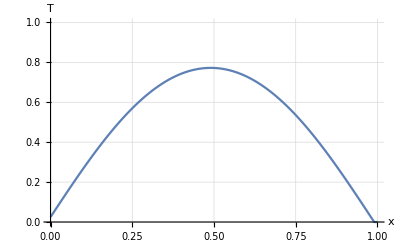

```mathematica
(*Попытка явно посчитать ряд из аналитического решения, плохо приближает граничные условия*)
f[x_]:=1;
phi1[t_]:=0;
phi2[t_]:=0;
recursion = 10;(*Длина ряда*)
temp=Table[0,{n+1}];
time=Tv;
k=70;
For[p=1,
p<n,
p++,
{
sum=0;
For[
i=1,
i<recursion,
i++,
{
sum +=2*Sin[Pi*i*p*dx]*E^(-Pi^2*i^2*kappa*time)*(Integrate[f[c]*Sin[Pi*i*c],{c,0,1}]+i*kappa*Pi*Integrate[E^(Pi^2*i^2*kappa*l)*(phi1[l]-(-1)^n*phi2[l]),{l,0,time}]);
}
];
temp[[p]]=sum;
}]

ListPlot[temp,DataRange->{0,L},PlotRange->{{0,1},{0,1}},AxesLabel->{"x","T"},
GridLines->Automatic,Joined->True]
```